```mathematica
Tmax=5000;
immi=0.15;
emmi=0.2;
n0=40;
k=200;
```

```mathematica
Timing[tab=Table[n=n0;Table[n=n+If[Random[]<immi,1,0]-If[Random[]<emmi,1,0];
n=If[n<0,0,n],{t,1,Tmax}],{i,1,k}];
tabmean=Thread[Mean[tab]];]
```

{2.529,Null}

Here is what the means of populations looks like

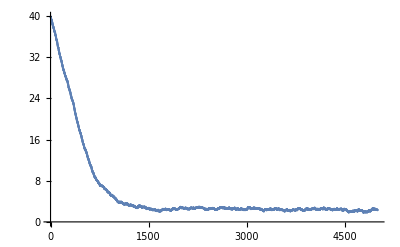

```mathematica
ListPlot[tabmean,PlotRange->All]
```

And here is a single run

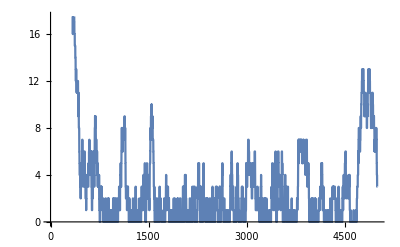

```mathematica
ListPlot[tab[[1]],Joined->True]
```